```mathematica
WW1={{0.25,-0.000013194480950147668},{0.5,0.00031019501993460527},{0.75,0.002717604576925877},{1.,0.02367018706977363},{1.25,0.19578871067225387},{1.5,0.5559503122153263},{1.75,0.9460873538144916},{2.,1.145759239104823},{2.25,1.2325292874917195},{2.5,1.2768727953183623},{2.75,1.2825075270726898},{3.,1.2573453205089582}};
```

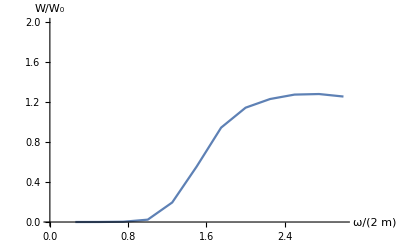

```mathematica
ListLinePlot[Re[WW1],PlotRange->{{0,3},{0,2}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

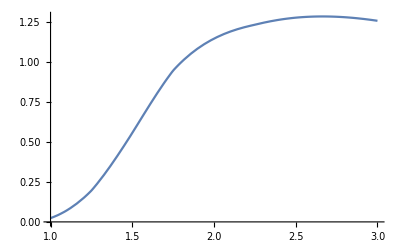

```mathematica
WWW1=Interpolation[WW1];
Plot[WWW1[x],{x,1,3}]
```

```mathematica
WW2={{0.25,0.},{0.5,0.},{0.75,0.},{1.,0.},{1.25,0.00936722114783678},{1.5,0.0597452442521996},{1.75,0.16377818228531726},{2.,0.31265018931986666},{2.25,0.4852875215703426},{2.5,0.6639322562477769},{2.75,0.8224030426851879},{3.,0.9645419991274135}};
```

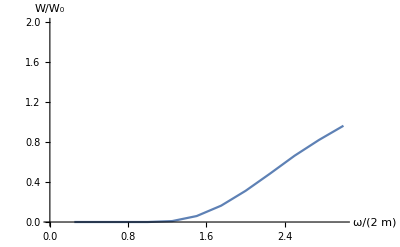

```mathematica
ListLinePlot[Re[WW2],PlotRange->{{0,3},{0,2}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

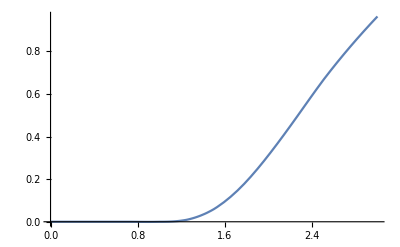

```mathematica
WWW2=Interpolation[WW2];
Plot[WWW2[x],{x,0,3}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

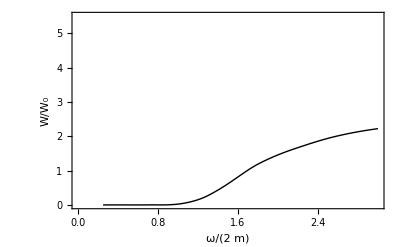

```mathematica
Plot[{WWW1[x]+WWW2[x],WW1220[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick,Dashed}},PlotRange->{{0,3},{0,5.5}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->{Bold,24}]
```

```mathematica
WW11={{1.,0},{1.1,0.51},{1.2000000000000002,1.0266357922263716},{1.3000000000000003,1.6482998113796232},{1.4000000000000004,2.4009615896780053},{1.5000000000000004,2.940509341483505},{1.6000000000000005,3.4152576060038467},{1.7000000000000006,4.075195490132475},{1.8000000000000007,4.444865964928983},{1.9000000000000008,4.409005261342843},{2.000000000000001,4.036842588251251},{2.100000000000001,3.2136177819375553},{2.200000000000001,2.6818767092082805},{2.300000000000001,2.178391188434085},{2.4000000000000012,1.8029162418506428},{2.5,1.499451390812346},{2.6,1.2885371403504409},{2.7,1.0877168972087858},{2.8000000000000003,0.9626271767496124},{2.9000000000000004,0.8881653979175421},{3.,0.8575513475745847}};
```

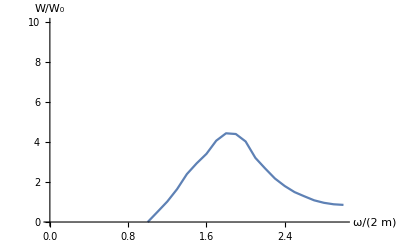

```mathematica
ListLinePlot[Re[WW11],PlotRange->{{0,3},{0,10}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

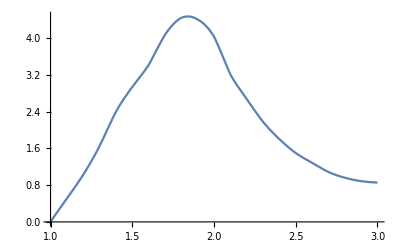

```mathematica
WWW11=Interpolation[WW11];
Plot[WWW11[x],{x,1,3}]
```

```mathematica
WW12={{1.,0.},{1.1,-0.0001535008684756593},{1.2000000000000002,-0.0023142499948259148},{1.3000000000000003,0.007737672102380029},{1.4000000000000004,0.023533130996765315},{1.5000000000000004,0.046267690116661105},{1.6000000000000005,0.07867685498186346},{1.7000000000000006,0.10163824726325799},{1.8000000000000007,0.1411307883642298},{1.9000000000000008,0.18193774389937464},{1.91,0.1859208397413663},{1.92,0.19015881693470116},{1.93,0.1943943885785327},{1.94,0.198151902430094745},{1.95,0.20309042549439016},{1.96,0.209656956909001},{1.97,0.21152745879764026},{1.98,0.217319564397641},{1.99,0.22977918813151274},{2.000000000000001,0.25189493458481854},{2.01,0.2203752961256955},{2.0199999999999996,0.21187301441899128},{2.0299999999999994,0.20683628428200104},{2.039999999999999,0.20335321243358342},{2.049999999999999,0.2007671971930456},{2.0599999999999987,0.19876683989923224},{2.0699999999999985,0.197177107963559},{2.0799999999999983,0.1958923720915257},{2.089999999999998,0.19484021093574574},{2.100000000000001,0.19397308322231552},{2.200000000000001,0.19039364510890372},{2.300000000000001,0.19013434283941982},{2.4000000000000012,0.1903424345967275},{2.5000000000000013,0.19012410578119432},{2.6000000000000014,0.1891658348002664},{2.7000000000000015,0.18734674440578936},{2.8000000000000016,0.18465441576606748},{2.9000000000000017,0.18112717068933262},{3.0000000000000018,0.1768349632286124}};
```

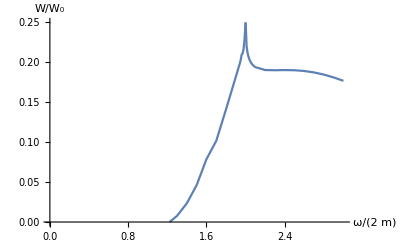

```mathematica
ListLinePlot[Re[WW12],PlotRange->{{0,3},{0,0.25}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

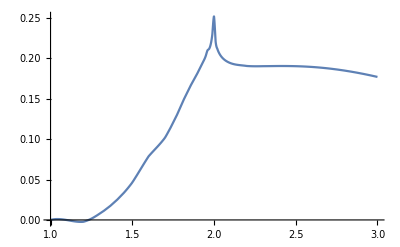

```mathematica
WWW12=Interpolation[WW12];
Plot[WWW12[x],{x,1,3}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

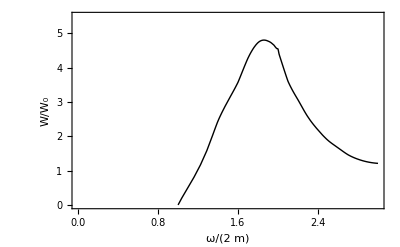

```mathematica
Plot[{WWW11[x]+2WWW12[x],WW1220[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick,Dashed}},PlotRange->{{0,3},{0,5.5}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->{Bold,24}]
```